```mathematica
{X,Y}={x,y}/.DSolve[{x'[t]==-c1*x[t]/c2+c1*(y[t]-x[t])/c2,y'[t]==-c1*(y[t]-x[t])/c2,x[0]==0,y[0]==1},{x,y},t]//FullSimplify//First
```

{Function[{t},(ⅇ^(-(3 c1 t)/(2 c2)-(√5 c1 t)/(2 c2)) (-1+ⅇ^((√5 c1 t)/c2)))/(√5)],Function[{t},1/10 ⅇ^(-(3 c1 t)/(2 c2)-(√5 c1 t)/(2 c2)) (5-√5+5 ⅇ^((√5 c1 t)/c2)+√5 ⅇ^((√5 c1 t)/c2))]}

```mathematica
Manipulate[Plot[Evaluate[{X[t],Y[t]}/.{c1->a,c2->b}],{t,0,10},PlotRange->{0,1},PlotStyle->Thick,Filling->{1->{2}}],{{a,1.3,"c1"},1,3,Appearance->"Labeled"},{{b,2.5,"c2"},1,3,Appearance->"Labeled"}]
```

```mathematica
(* A1 (->)^k11 A2 (->)^k12 B (->)^k2 C *)
(* A1 (->)^k11 A2 (->)^k12 B (->)^k3 D *)
{A1, A2,B}={a1, a2, b}/.DSolve[{
a1'[t]==-k11*a1[t],
a2'[t]==k11*a1[t]-k12*a2[t],
b'[t]==k12*a2[t]-k2*b[t],
a1[0]==1, a2[0]==0, b[0]==0},{a1,a2,b},t,Assumptions->k11>k2&& k12>k2]//FullSimplify//First
```

{Function[{t},ⅇ^(-k11 t)],Function[{t},-(ⅇ^(-k11 t-k12 t) (-ⅇ^(k11 t)+ⅇ^(k12 t)) k11)/(k11-k12)],Function[{t},(ⅇ^(-k11 t-k12 t-k2 t) k11 k12 (ⅇ^(k11 t+k12 t) k11-ⅇ^(k11 t+k2 t) k11-ⅇ^(k11 t+k12 t) k12+ⅇ^(k12 t+k2 t) k12+ⅇ^(k11 t+k2 t) k2-ⅇ^(k12 t+k2 t) k2))/((k11-k12) (k11-k2) (k12-k2))]}

```mathematica
(ⅇ^(-k11 t-k12 t-k2 t) k11 k12 (ⅇ^(k11 t+k12 t) k11-ⅇ^(k11 t+k2 t) k11-ⅇ^(k11 t+k12 t) k12+ⅇ^(k12 t+k2 t) k12+ⅇ^(k11 t+k2 t) k2-ⅇ^(k12 t+k2 t) k2))/((k11-k12) (k11-k2) (k12-k2))
```

```mathematica
(* A (->)^kk A' (->)^kk B (->)^k1 C*)
(* A (->)^kk A' (->)^kk B (->)^k1 C*)
{A,B}={a,b}/.DSolve[{
a'[t]==-k1*a[t],
b'[t]==k1*a[t]-k2*b[t],
a[0]==1,b[0]==0},{a,b},t,Assumptions->k1>k2]//FullSimplify//First
```

{Function[{t},ⅇ^(-k1 t)],Function[{t},-(ⅇ^(-k1 t-k2 t) (-ⅇ^(k1 t)+ⅇ^(k2 t)) k1)/(k1-k2)]}

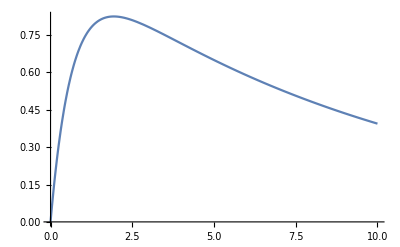

```mathematica
Plot[Evaluate[B[t]/.{k1->1.5,k2->0.1}],{t,0,10}]
```

```mathematica
Integrate[(ⅇ^(-k1 td)) *(ⅇ^(-(t-td)^2/(2 sigma^2)))/(√(2 π) sigma),{td, 0, ∞}, Assumptions->sigma>0]//FullSimplify
```

1/2 ⅇ^(1/2 k1 (k1 sigma^2-2 t)) (1+Erf[(-k1 sigma^2+t)/(√2 sigma)])

```mathematica
(k1 (ⅇ^(1/2 k2 (k2 sigma^2-2 t)) (1+Erf[(-k2 sigma^2+t)/(√2 sigma)])+ⅇ^(1/2 k1 (k1 sigma^2-2 t)) (-2+Erfc[(-k1 sigma^2+t)/(√2 sigma)])))/(2 (k1-k2))
```

(k1 (ⅇ^(1/2 k2 (k2 sigma^2-2 t)) (1+Erf[(-k2 sigma^2+t)/(√2 sigma)])+ⅇ^(1/2 k1 (k1 sigma^2-2 t)) (-2+Erfc[(-k1 sigma^2+t)/(√2 sigma)])))/(2 (k1-k2))

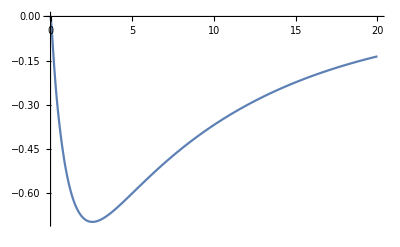

```mathematica
Plot[Evaluate[%/. {sigma->0.135, k1->1, k2->0.1}], {t,0,20}]
```

```mathematica
Manipulate[Plot[Evaluate[{A[t],B[t]}/.{k1->c1,k2->c2}],{t,0,3},PlotRange->{0,1},PlotStyle->Thick,Filling->Axis],{{c1,1.3,"k1"},0.1,5,Appearance->"Labeled"},{{c2,3,"k2"},0.1,5,Appearance->"Labeled"}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ⅇ^(-10. t) ComplexInfinity encountered.

```mathematica
PDF[NormalDistribution[0,σ],t]
```

(ⅇ^(-t^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
{A1,A2, B}=
{a1,a2, b}/.DSolve[{
a1'[t]==-kk*a1[t],
a2'[t]==-kk*a2[t]+kk*a1[t],
b'[t]==kk*a2[t]-k1*b[t],
a1[0]==1,a2[0]==0,b[0]==0},{a1,a2,b},t]//FullSimplify//First
```

{Function[{t},ⅇ^(-kk t)],Function[{t},ⅇ^(-kk t) kk t],Function[{t},(ⅇ^(-k1 t-kk t) kk^2 (-ⅇ^(k1 t)+ⅇ^(kk t)+ⅇ^(k1 t) k1 t-ⅇ^(k1 t) kk t))/(k1-kk)^2]}

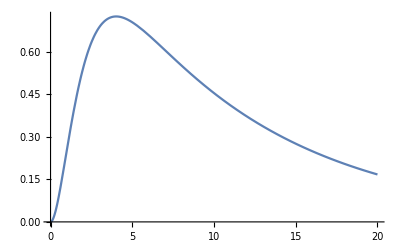

```mathematica
Plot[Evaluate[{B[t]}/.{kk->1, k1->0.1}], {t, 0, 20}]
```

```mathematica
(* A (->)^kk A' (->)^kk B (->)^k1 C *)
ClearAll
{A1,A2, B}=
{a1,a2, b}/.DSolve[{
a1'[t]==-kk*a1[t],
a2'[t]==-kk*a2[t]+kk*a1[t],
b'[t]==kk*a2[t]-k1*b[t],
a1[0]==1,a2[0]==0,b[0]==0},{a1,a2,b},t]//FullSimplify//First
```

ClearAll

{Function[{t},ⅇ^(-kk t)],Function[{t},ⅇ^(-kk t) kk t],Function[{t},(ⅇ^(-k1 t-kk t) kk^2 (-ⅇ^(k1 t)+ⅇ^(kk t)+ⅇ^(k1 t) k1 t-ⅇ^(k1 t) kk t))/(k1-kk)^2]}

```mathematica
Plot[Evaluate[{B[t]}/.{kk->1,kb->2, k1->0.1}], {t, 0, 20}]
```

-Graphics-

```mathematica
(* A (->)^kk A' (->)^kk B (->)^kk C*)
{A1,A2, B}=
{a1,a2, b}/.DSolve[{
a1'[t]==-kk*a1[t],
a2'[t]==-kk*a2[t]+kk*a1[t],
b'[t]==kk*a2[t]-kk*b[t],
a1[0]==1,a2[0]==0,b[0]==0},{a1,a2,b},t]//FullSimplify//First
```

{Function[{t},ⅇ^(-kk t)],Function[{t},ⅇ^(-kk t) kk t],Function[{t},1/2 ⅇ^(-kk t) kk^2 t^2]}

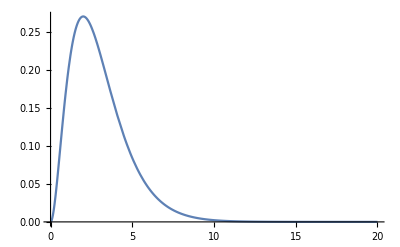

```mathematica
Plot[Evaluate[{B[t]}/.{kk->1}], {t, 0, 20}]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
(* A (->)^kk A' (->)^kk B (->)^k1 C*)
(* A (->)^kk-------> B (->)^k1 C*)
ClearAll
{A1,A2, B}=
{a1,a2, b}/.DSolve[{
a1'[t]==-kk*a1[t],
a2'[t]==-kk*a2[t]+kk*a1[t],
b'[t]==kk*a2[t]+kk*a1[t]-k1*b[t],
a1[0]==1,a2[0]==0,b[0]==0},{a1,a2,b},t]//FullSimplify//First
```

ClearAll

{Function[{t},ⅇ^(-kk t)],Function[{t},ⅇ^(-kk t) kk t],Function[{t},-(ⅇ^(-k1 t-kk t) kk (-ⅇ^(k1 t) k1+ⅇ^(kk t) k1+2 ⅇ^(k1 t) kk-2 ⅇ^(kk t) kk-ⅇ^(k1 t) k1 kk t+ⅇ^(k1 t) kk^2 t))/(k1-kk)^2]}

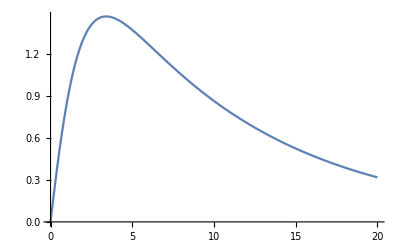

```mathematica
Plot[Evaluate[{B[t]}/.{kk->1, k1->0.1}], {t, 0, 20}]
```

```mathematica
(* A (->)^kk1 A' (->)^kk1 B (->)^k1 C*)
(* A (->)^kk2-------> B (->)^k1 C*)
ClearAll
{A1,A2, B}=
{a1,a2, b}/.DSolve[{
a1'[t]==-(kk3)*a1[t],
a2'[t]==-kk1*a2[t]+kk1*a1[t],
b'[t]==kk1*a2[t]+kk2*a1[t]-k1*b[t],
a1[0]==1,a2[0]==0,b[0]==0},{a1,a2,b},t]//FullSimplify//First
```

ClearAll

{Function[{t},ⅇ^((-kk1-kk2) t)],Function[{t},-(ⅇ^(-kk1 t) (-1+ⅇ^(kk1 t+(-kk1-kk2) t)) kk1)/kk2],Function[{t},-1/((k1-kk1) (k1-kk1-kk2) kk2)ⅇ^(-k1 t-kk1 t) (-ⅇ^(k1 t) k1 kk1^2+ⅇ^(k1 t+kk1 t+(-kk1-kk2) t) k1 kk1^2+ⅇ^(k1 t) kk1^3-ⅇ^(k1 t+kk1 t+(-kk1-kk2) t) kk1^3+ⅇ^(k1 t) kk1^2 kk2-ⅇ^(kk1 t) kk1^2 kk2+ⅇ^(kk1 t) k1 kk2^2-ⅇ^(k1 t+kk1 t+(-kk1-kk2) t) k1 kk2^2-ⅇ^(kk1 t) kk1 kk2^2+ⅇ^(k1 t+kk1 t+(-kk1-kk2) t) kk1 kk2^2)]}

```mathematica
ClearAll
Integrate[td*Exp[-kk*td] *(ⅇ^(-(t-td)^2/(2 sigma^2)))/(√(2 π) sigma),{td, 0, ∞}, Assumptions->sigma>0]//FullSimplify
```

ClearAll

(ⅇ^(-t^2/(2 sigma^2)) (√2 sigma-ⅇ^(((-kk sigma^2+t)^2)/(2 sigma^2)) √π (kk sigma^2-t) Erfc[(kk sigma^2-t)/(√2 sigma)]))/(2 √π)

```mathematica
Integrate[(ⅇ^(-(td)^2/(2 w^2)))/(√(2 π) w) *(ⅇ^(-(t-td)^2/(2 sigma^2)))/(√(2 π) sigma),{td, 0, ∞}, Assumptions->sigma>0]//FullSimplify
```

ConditionalExpression[(ⅇ^(-t^2/(2 (sigma^2+w^2))) (1+Erf[t/(√2 sigma^2 √(1/sigma^2+1/w^2))]))/(2 √(2 π) sigma √(1/sigma^2+1/w^2) w),(Re[t]≥0&&sigma^2 Re[1/w^2]>-1)||(Re[t]<0&&sigma^2 Re[1/w^2]≥-1)]

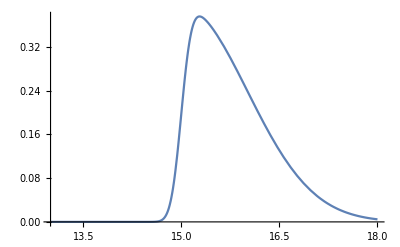

```mathematica
Plot[Evaluate[(ⅇ^(-(t-t0)^2/(2 (sigma^2+w^2))) (1+Erf[(t-t0)/(√2 sigma^2 √(1/sigma^2+1/w^2))]))/(2 √(2 π) sigma √(1/sigma^2+1/w^2) w)/.{sigma->0.125, w->1, t0-> 15}], {t, 13, 18}, PlotRange->All]
```

```mathematica
(* A -^kk-> A' -^kk-> B -^k1-> C *)
(* A -^kk-> A' -^kk-> B -^k2-> D*)
ClearAll
{A1,A2, B1, B2}=
{a1,a2, b1, b2}/.DSolve[{
a1'[t]==-kk*a1[t],
a2'[t]==-kk*a2[t]+kk*a1[t],
b1'[t]==kk*a2[t]-k1*b1[t],
b2'[t] == kk*a2[t] - k2*b2[t],
a1[0]==1,a2[0]==0,b1[0]==0, b2[0]== 0},{a1,a2,b1, b2},t]//FullSimplify//First
```

ClearAll

{Function[{t},ⅇ^(-kk t)],Function[{t},ⅇ^(-kk t) kk t],Function[{t},(ⅇ^(-k1 t-kk t) kk^2 (-ⅇ^(k1 t)+ⅇ^(kk t)+ⅇ^(k1 t) k1 t-ⅇ^(k1 t) kk t))/(k1-kk)^2],Function[{t},(ⅇ^(-k2 t-kk t) kk^2 (-ⅇ^(k2 t)+ⅇ^(kk t)+ⅇ^(k2 t) k2 t-ⅇ^(k2 t) kk t))/(k2-kk)^2]}

```mathematica
(*  *)
(* D*)
ClearAll
{A1}=
{a1}/.DSolve[{
a1'[t]==-k1*a1[t]- k2*a1[t]^2,
a1[0]==a10},{a1},t]//Reduce
```

ClearAll

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Reduce::naqs: {Function[{t},(a10 k1)/(ⅇ^Times[«2»] k1-a10 k2+a10 ⅇ^Times[«2»] k2)]} is not a quantified system of equations and inequalities.

Set::shape: Lists {A1} and Reduce[{{Function[{t},(a10 k1)/(Times[«2»]+Times[«3»]+Times[«3»])]}}] are not the same shape.

Reduce[{{Function[{t},(a10 k1)/(ⅇ^(k1 t) k1-a10 k2+a10 ⅇ^(k1 t) k2)]}}]

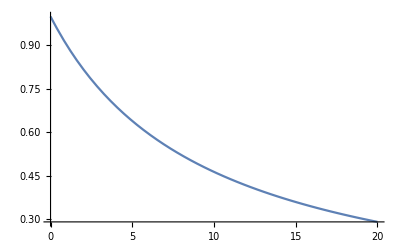

```mathematica
Plot[Evaluate[{A1[t]}/.{a10->20, k1->0.01, k2->0.1}], {t, 0, 20}]
```

```mathematica
(*  *)
(* *)
ClearAll
{A, B1, B2, B3, B4}=
{a, b1, b2, b3, b4}/.DSolve[{
a'[t] ==-kc*a[t],
b1'[t] == kc*a[t] - k1*b1[t],
b2'[t] == kc*a[t] - k2*b2[t],
b3'[t] == kc*a[t] - k3*b3[t]^2,
b4'[t] == kc*a[t] - k4*b4[t]^2,
a[0]==a0, b1[0]==0, b2[0]==0, b3[0]==0, b4[0]==0},
{a, b1, b2, b3, b4},t]
```

```mathematica
(*  *)
(* *)
ClearAll
{A, B1,  B3}=
{a, b1, b3}/.DSolve[{
a'[t] ==-kc*a[t],
b1'[t] == kc*a[t] - k1*b1[t],
b3'[t] == kc*a[t] - k3*b3[t]^2,
a[0]==a0, b1[0]==0,  b3[0]==0},
{a, b1, b3},t]
```

ClearAll

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is √k3 (-4 a0+(kc (InverseFunction[BesselK,2,2][1,BesselK[1,2 Power[«2»] Power[«2»] Power[«2»]]])^2)/k3) == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 4 a0 k3-kc (InverseFunction[BesselK,2,2][1,BesselK[1,(2 √k3 √C[«1»])/(√kc)]])^2 == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is (4 a0 k3)/(√kc)-√kc (InverseFunction[BesselK,2,2][1,BesselK[1,(2 √k3 √C[«1»])/(√kc)]])^2 == 0.

General::stop: Further output of Solve::incnst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Set::shape: Lists {A,B1,B3} and {{Function[{t},a0 ⅇ^(-kc t)],Function[{t},(a0 ⅇ^(-k1 t) (-1+ⅇ^(Plus[«2»] t)) kc)/(k1-kc)],Function[{t},(-√a0 √Power[«2»] √kc BesselI[1,Times[«5»]] BesselK[1,Times[«4»]]+√a0 √Power[«2»] √kc BesselI[1,Times[«4»]] BesselK[1,Times[«5»]])/(√k3 (BesselI[«2»] BesselK[«2»]+BesselI[«2»] BesselK[«2»]))]}} are not the same shape.

{{Function[{t},a0 ⅇ^(-kc t)],Function[{t},(a0 ⅇ^(-k1 t) (-1+ⅇ^((k1-kc) t)) kc)/(k1-kc)],Function[{t},(-√a0 √(ⅇ^(-kc t)) √kc BesselI[1,(2 √a0 √(ⅇ^(-kc t)) √k3)/(√kc)] BesselK[1,(2 √a0 √k3)/(√kc)]+√a0 √(ⅇ^(-kc t)) √kc BesselI[1,(2 √a0 √k3)/(√kc)] BesselK[1,(2 √a0 √(ⅇ^(-kc t)) √k3)/(√kc)])/(√k3 (BesselI[1,(2 √a0 √k3)/(√kc)] BesselK[0,(2 √a0 √(ⅇ^(-kc t)) √k3)/(√kc)]+BesselI[0,(2 √a0 √(ⅇ^(-kc t)) √k3)/(√kc)] BesselK[1,(2 √a0 √k3)/(√kc)]))]}}

```mathematica
(*  *)
(* D*)
ClearAll
{A1}=
{a1}/.DSolve[{
a1'[t]==k2*a1[t]^2,
a1[0]==a10},{a1},t]//Reduce
```

ClearAll

Reduce::naqs: {Function[{t},-a10/(-1+a10 k2 t)]} is not a quantified system of equations and inequalities.

Set::shape: Lists {A1} and Reduce[{{Function[{t},-a10/(-1+Times[«3»])]}}] are not the same shape.

Reduce[{{Function[{t},-a10/(-1+a10 k2 t)]}}]

```mathematica
(*  *)
(* *)
ClearAll
{A,  B3}=
{a, b3}/.DSolve[{
a'[t] ==-kc*a[t],
b3'[t] == kc*a[t] - k3*b3[t]^2,
a[0]==a0,  b3[0]==0},
{a, b1, b3},t]
```

Correlation between two guassian laser pulses

```mathematica
Integrate[(ⅇ^(-(td)^2/(2 sig1^2)))/(√(2 π) sig1) *(ⅇ^(-(td - t+1)^2/(2 sig2^2)))/(√(2 π) sig2), {td, -∞, ∞}]
```

ConditionalExpression[(ⅇ^(-(-1+t)^2/(2 (sig1^2+sig2^2))))/(√(2 π) sig1 √(1/sig1^2+1/sig2^2) sig2),Re[1/sig1^2+1/sig2^2]≥0]

clearall

0.178359

0.127399

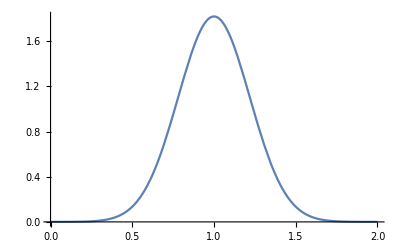

```mathematica
clearall
sig1 = 0.420 / 2.3548
sig2 = 0.3 / 2.3548
Plot[Integrate[(ⅇ^(-(td)^2/(2 sig1^2)))/(√(2 π) sig1) *(ⅇ^(-(td - t+1)^2/(2 sig2^2)))/(√(2 π) sig2),{td, -10, 10}], {t, 0,2}]
```

FWHM of pump-probe correlation is around 520 femtosecond

```mathematica
clearall
sig1 = 0.420 / 2.3548;
sig2 = 0.3 / 2.3548;
corrData = Table[Integrate[(ⅇ^(-(td)^2/(2 sig1^2)))/(√(2 π) sig1) *(ⅇ^(-(td - t+1)^2/(2 sig2^2)))/(√(2 π) sig2),{td, -10, 10}], {t, 0,2, 0.1}];
```

clearall

```mathematica
corrData
```

{0.0000549799,0.000397177,0.00233005,0.0111007,0.0429473,0.134935,0.344282,0.713356,1.20033,1.6402,1.82011,1.6402,1.20033,0.713356,0.344282,0.134935,0.0429473,0.0111007,0.00233005,0.000397177,0.0000549799}

```mathematica
Fit[%49,{1,x,x^2,x^3},x]
```

-0.72165+0.31248 x-0.0142036 x^2-2.14579×10^-18 x^3

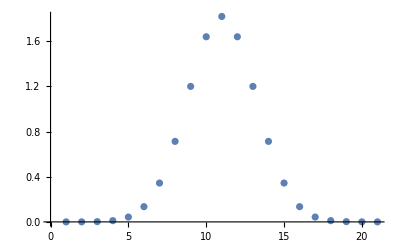

```mathematica
ListPlot[%49]
```

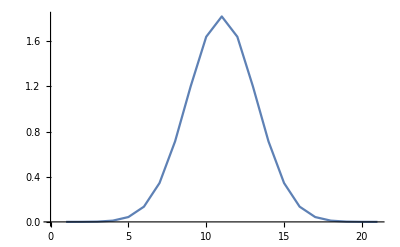

```mathematica
ListLinePlot[%49]
```

```mathematica
Export["pulsecorr.xls", corrData, "XLS"]
```

pulsecorr.xls

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["pulsecorr.xls"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["pulsecorr.xls"]]]
```

```mathematica
Export [corrData, "CSV"]
```

Export::chtype: First argument 0.0000549799 is not a valid file specification.

Export::chtype: First argument 0.000397177 is not a valid file specification.

Export::chtype: First argument 0.00233005 is not a valid file specification.

General::stop: Further output of Export::chtype will be suppressed during this calculation.

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
(*Tryint to find out the nature of double pulse from TAM*)
{A,B}={a,b}/.DSolve[{
a'[t]==-k1*a[t],
b'[t]==k1*a[t]-k2*b[t],
a[0]==1,b[0]==0},{a,b},t,Assumptions->k1>k2]//FullSimplify//First
```

{Function[{t},ⅇ^(-k1 t)],Function[{t},-(ⅇ^(-k1 t-k2 t) (-ⅇ^(k1 t)+ⅇ^(k2 t)) k1)/(k1-k2)]}

```mathematica
Manipulate[Plot[Evaluate[{A[t],B[t]}/.{k1->c1,k2->c2}],{t,0,3},PlotRange->{0,1},PlotStyle->Thick,Filling->Axis],{{c1,1.3,"k1"},0.1,5,Appearance->"Labeled"},{{c2,3,"k2"},0.1,5,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[ampa (ⅇ^(-ka1 t-ka2 t) (+ⅇ^(ka1 t)-ⅇ^(ka2 t)) ka1)/(ka1-ka2) +
ampb (ⅇ^(-kb1 t-kb2 t) (+ⅇ^(kb1 t)-ⅇ^(kb2 t)) kb1)/(kb1-kb2), {t, 0,30}], 
{{ampa, 1.9, "ampa"},-10, 10, Appearance->"Labeled"},
{{ka1, 8.41, "ka1"}, 0.1, 10, Appearance->"Labeled"},
{ {ka2, 6.5, "ka2"}, 0.1, 10, Appearance->"Labeled"},
{{ampb, 2.06, "ampb"},-10, 10, Appearance->"Labeled"}, 
{{kb1, 1.24, "kb1"}, 0.001, 10, Appearance->"Labeled"},
{{kb2, 0.32, "kb2"}, 0.001, 10, Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[ampa (ⅇ^(-kb1 t-ka2 t) (+ⅇ^(kb1 t)-ⅇ^(ka2 t)) kb1)/(kb1-ka2)+
ampb (ⅇ^(-kb1 t-kb2 t) (+ⅇ^(kb1 t)-ⅇ^(kb2 t)) kb1)/(kb1-kb2), {t, 0,30}], 
{{ampa, 1.9, "ampa"},-10, 10, Appearance->"Labeled"},
{ {ka2, 6.5, "ka2"}, 0.1, 10, Appearance->"Labeled"},
{{ampb, 2.06, "ampb"},-10, 10, Appearance->"Labeled"}, 
{{kb1, 1.24, "kb1"}, 0.001, 10, Appearance->"Labeled"},
{{kb2, 0.32, "kb2"}, 0.001, 10, Appearance->"Labeled"}]
```

# Dealing with the negative positive signal

ClearAll

0.5

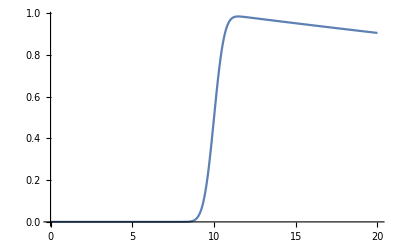

```mathematica
ClearAll
k1 = 0.01;
sigma = 0.5
t0 = 10;
Plot[1/2 ⅇ^(1/2 k1 (k1 sigma^2-2 (t-t0))) (1+Erf[(-k1 sigma^2+(t-t0))/(√2 sigma)]), {t, 0,20 }]
```

```mathematica
Integrate[Exp[-k1*td] *(ⅇ^(-(t-td)^2/(2 sigma^2)))/(√(2 π) sigma),{td, 0, ∞}, Assumptions->sigma>0]
```

1/2 ⅇ^(1/2 k1 (k1 sigma^2-2 t)) (1+Erf[(-k1 sigma^2+t)/(√2 sigma)])

```mathematica
ClearAll
sigma = 0.5;
Manipulate[Plot[ampa 1/2 ⅇ^(1/2 ka (ka sigma^2-2 (t-t0a))) (1+Erf[(-ka sigma^2+(t-t0a))/(√2 sigma)])+
ampb 1/2 ⅇ^(1/2 kb (k1 sigma^2-2 (t-t0b))) (1+Erf[(-kb sigma^2+(t-t0b))/(√2 sigma)]), {t, 0,50}, 
PlotRange->All], 
{{ampa, 3.16, "ampa"},-10, 10, Appearance->"Labeled"},
{ {ka, 0.05, "ka"}, 0.001, 0.05, Appearance->"Labeled"},
{{t0a, 1.77, "t0a"}, 0.1, 5, Appearance-> "Labeled"},
{{ampb, -2.12, "ampb"},-10, 10, Appearance->"Labeled"}, 
{{kb,0.13, "kb"}, 0.005,2, Appearance->"Labeled"},
{{t0b, 2, "t0b"}, 0.1, 2, Appearance->"Labeled"}]
```

ClearAll

```mathematica
ClearAll
sigma = 0.5;
Manipulate[Plot[ampa 1/2 ka1/(ka2-ka1)(ⅇ^(1/2 ka1 (ka1 sigma^2-2 (t-t0a))) (1+Erf[(-ka1 sigma^2+(t-t0a))/(√2 sigma)])- 
ⅇ^(1/2 ka2 (ka2 sigma^2-2 (t-t0a))) (1+Erf[(-ka2 sigma^2+(t-t0a))/(√2 sigma)]))+
ampb 1/2 ⅇ^(1/2 kb (k1 sigma^2-2 (t-t0b))) (1+Erf[(-kb sigma^2+(t-t0b))/(√2 sigma)]), {t, 0,50}, 
PlotRange->All], 
{{ampa, 3.16, "ampa"},-10, 10, Appearance->"Labeled"},
{{ka1,0.05, "ka1"},0.001, 0.05, Appearance->"Labeled"},
{ {ka2, 0.5, "ka2"}, 0.005, 1, Appearance->"Labeled"},
{{t0a, 1.77, "t0a"}, 0.1, 5, Appearance-> "Labeled"},
{{ampb, -2.12, "ampb"},-10, 10, Appearance->"Labeled"}, 
{{kb,0.13, "kb"}, 0.005,2, Appearance->"Labeled"},
{{t0b, 2, "t0b"}, 0.1, 2, Appearance->"Labeled"}]
```

ClearAll

```mathematica
ClearAll
sigma = 0.5;
t0 = 5
Manipulate[Plot[ampa 1/2 ⅇ^(1/2 ka (ka sigma^2-2 (t-t0))) (1+Erf[(-ka sigma^2+(t-t0))/(√2 sigma)])+
ampb 1/2 ⅇ^(1/2 kb (k1 sigma^2-2 (t-t0))) (1+Erf[(-kb sigma^2+(t-t0))/(√2 sigma)]), {t, 0,50}, 
PlotRange->All], 
{{ampa, 3.16, "ampa"},-10, 10, Appearance->"Labeled"},
{ {ka, 0.05, "ka"}, 0.001, 0.05, Appearance->"Labeled"},
{{ampb, -2.12, "ampb"},-10, 10, Appearance->"Labeled"}, 
{{kb,0.13, "kb"}, 0.005,2, Appearance->"Labeled"}]
```

ClearAll

5

```mathematica
ClearAll
sigma = 0.5;
ampa = 1;
ka = 0.01;
t0a = 5;
ampb = -0.5;
kb = 0.2;
t0b = 4;
Plot[ampa 1/2 ⅇ^(1/2 ka (ka sigma^2-2 (t-t0a))) (1+Erf[(-ka sigma^2+(t-t0a))/(√2 sigma)])+
ampb 1/2 ⅇ^(1/2 kb (k1 sigma^2-2 (t-t0b))) (1+Erf[(-kb sigma^2+(t-t0b))/(√2 sigma)]), {t, 0,20}]
```

ClearAll

-Graphics-

```mathematica
ClearAll
sigma = 0.5;
t0 = 5;
Manipulate[Plot[ampa 1/2 ka1/(ka2-ka1)(ⅇ^(1/2 ka1 (ka1 sigma^2-2 (t-t0))) (1+Erf[(-ka1 sigma^2+(t-t0))/(√2 sigma)])- 
ⅇ^(1/2 ka2 (ka2 sigma^2-2 (t-t0))) (1+Erf[(-ka2 sigma^2+(t-t0))/(√2 sigma)]))+
ampb 1/2 ⅇ^(1/2 kb (kb sigma^2-2 (t-t0))) (1+Erf[(-kb sigma^2+(t-t0))/(√2 sigma)])+
ampTh (ⅇ^(-(t-t0)^2/(2 wTh^2)))/(√(2 π) wTh), {t, 0,50}, 
PlotRange->All], 
{{ampa, 2.34, "ampa"},0, 10, Appearance->"Labeled"},
{{ka1,0.0133, "ka1"},0.001, 0.05, Appearance->"Labeled"},
{{ka2, 0.208, "ka2"}, 0.005, 1, Appearance->"Labeled"},
{{ampb, 0.18, "ampb"},0, 10, Appearance->"Labeled"}, 
{{kb,0.492, "kb"}, 0.05,2, Appearance->"Labeled"},
{{wTh, 0.62, "Thermal Width"}, 0.01, 5, Appearance->"Labeled"},
{{ampTh, -0.06, "Thermal Amp"},-5, 5, Appearance->"Labeled"}]
```

ClearAll

```mathematica
ClearAll
sigma = 0.5;
t0 = 5;
Manipulate[Plot[ampa 1/2 ka/(kb-ka)(ⅇ^(1/2 ka (ka sigma^2-2 (t-t0))) (1+Erf[(-ka sigma^2+(t-t0))/(√2 sigma)])- 
ⅇ^(1/2 kb (kb sigma^2-2 (t-t0))) (1+Erf[(-kb sigma^2+(t-t0))/(√2 sigma)]))+
ampb 1/2 ⅇ^(1/2 kb (kb sigma^2-2 (t-t0))) (1+Erf[(-kb sigma^2+(t-t0))/(√2 sigma)])+
ampTh (ⅇ^(-(t-t0)^2/(2 wTh^2)))/(√(2 π) wTh), {t, 0,50}, 
PlotRange->All], 
{{ampa, 2.34, "ampa"},0, 10, Appearance->"Labeled"},
{{ka,0.0133, "ka"},0.001, 0.05, Appearance->"Labeled"},
{{ampb, 0.18, "ampb"},0, 10, Appearance->"Labeled"}, 
{{kb,0.492, "kb"}, 0.05,2, Appearance->"Labeled"},
{{wTh, 0.62, "Thermal Width"}, 0.01, 5, Appearance->"Labeled"},
{{ampTh, -0.06, "Thermal Amp"},-5, 5, Appearance->"Labeled"}]
```

ClearAll

```mathematica
ClearAll
sigma = 0.5;
t0 = 5;
Manipulate[Plot[ampa 1/2 (ⅇ^(1/2 ka1 (ka1 sigma^2-2 (t-t0))) (1+Erf[(-ka1 sigma^2+(t-t0))/(√2 sigma)])+
ⅇ^(1/2 ka2 (ka2 sigma^2-2 (t-t0))) (1+Erf[(-ka2 sigma^2+(t-t0))/(√2 sigma)]))+
ampTh (ⅇ^(-(t-t0)^2/(2 wTh^2)))/(√(2 π) wTh), {t, 0,50}, 
PlotRange->All], 
{{ampa, 2.34, "ampa"},0, 10, Appearance->"Labeled"},
{{ka1,0.0133, "ka1"},0.001, 0.05, Appearance->"Labeled"},
{{ka2, 0.208, "ka2"}, 0.005, 1, Appearance->"Labeled"},
{{wTh, 0.62, "Thermal Width"}, 0.01, 5, Appearance->"Labeled"},
{{ampTh, -0.06, "Thermal Width"},-5, 5, Appearance->"Labeled"}]
```

ClearAll

```mathematica
ClearAll
sigma = 0.5;
t0 = 5;
Manipulate[Plot[ampa 1/2 ⅇ^(1/2 ka(ka sigma^2-2 (t-t0))) (1+Erf[(-ka sigma^2+(t-t0))/(√2 sigma)])+
ampb 1/2 ⅇ^(1/2 kb (kb sigma^2-2 (t-t0))) (1+Erf[(-kb sigma^2+(t-t0))/(√2 sigma)])+
ampTh (ⅇ^(-(t-t0)^2/(2 wTh^2)))/(√(2 π) wTh), {t, 0,50}, 
PlotRange->All], 
{{ampa, 2.34, "ampa"},0, 10, Appearance->"Labeled"},
{{ka,0.0133, "ka1"},0.001, 0.05, Appearance->"Labeled"},
{{ampb, 0.18, "ampb"},0, 10, Appearance->"Labeled"}, 
{{kb,0.492, "kb"}, 0.05,2, Appearance->"Labeled"},
{{wTh, 0.62, "Thermal Width"}, 0.01, 5, Appearance->"Labeled"},
{{ampTh, -0.06, "Thermal Width"},-5, 5, Appearance->"Labeled"}]
```

ClearAll

```mathematica
ClearAll
sigma = 0.5;
(*t0 = 5;*)
Manipulate[Plot[ampa 1/2 ka1/(ka2-ka1)(ⅇ^(1/2 ka1 (ka1 sigma^2-2 (t-t0a))) (1+Erf[(-ka1 sigma^2+(t-t0a))/(√2 sigma)])- 
ⅇ^(1/2 ka2 (ka2 sigma^2-2 (t-t0a))) (1+Erf[(-ka2 sigma^2+(t-t0a))/(√2 sigma)]))+
ampb 1/2 kb1/(kb2-kb1)(ⅇ^(1/2 kb1 (kb1 sigma^2-2 (t-t0b))) (1+Erf[(-kb1 sigma^2+(t-t0b))/(√2 sigma)])- 
ⅇ^(1/2 kb2 (kb2 sigma^2-2 (t-t0b))) (1+Erf[(-kb2 sigma^2+(t-t0b))/(√2 sigma)]))+
ampTh (ⅇ^(-(t-t0b)^2/(2 wTh^2)))/(√(2 π) wTh), {t, 0,50}, 
PlotRange->All], 
{{ampa, 2.34, "ampa"},0, 10, Appearance->"Labeled"},
{{ka1,0.0133, "ka1"},0.001, 0.05, Appearance->"Labeled"},
{{ka2, 0.208, "ka2"}, 0.005, 1, Appearance->"Labeled"},
{{t0a,5, "t0a"}, 0.0,20, Appearance->"Labeled"},
{{ampb, 0.18, "ampb"},0, 10, Appearance->"Labeled"}, 
{{kb1,0.05, "kb1"}, 0.001,0.05, Appearance->"Labeled"},
{{kb2,0.5, "kb2"}, 0.005,1, Appearance->"Labeled"},
{{t0b,15, "t0b"}, 0.0,20, Appearance->"Labeled"},
{{wTh, 0.62, "Thermal Width"}, 0.01, 5, Appearance->"Labeled"},
{{ampTh, -0.06, "Thermal Amp"},-5, 5, Appearance->"Labeled"}]
```

ClearAll

General::munfl: Exp[-727.652] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-791.792] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-858.641] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-727.652] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-791.792] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-858.641] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-727.652] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-791.792] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-858.641] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-727.652] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-791.792] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-858.641] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
ClearAll;
sigma = 0.5;
tc = 2;
Manipulate[Plot[a1*(ⅇ^(-(t-tc)^2/(2 sigma^2)))/(√(2 π) sigma)+a2*(ⅇ^(-(t-(tc+1*sigma))^2/(2 sigma^2)))/(√(2 π) sigma), {t, 0, 10}, PlotRange->All],
{{a1, -1, "Amplitude"},-1, 0, Appearance->"Labeled"},
{{a2, 1, "Amplitude"}, 0, 1, Appearance-> "Labeled"}]
```

```mathematica
(ⅇ^(-(td)^2/(2 sig1^2)))/(√(2 π) sig1)
```

```mathematica
Names["Global`*"]
```

{}

```mathematica
?Global`*
```

```mathematica
Clear["Global`*"]
```

```mathematica
ClearGlobal[]:=(ClearAll["Global`*"];Clear[Derivative];);

RemoveGlobal[]:=(ClearGlobal[];Remove["Global`*"];);
```

```mathematica
Remove["Global`*"]
```

```mathematica
Quit[]
```